## Mods

```mathematica
<<PajaroLoco`
Options[EdgesStyleList2]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Hue[.85*vertexSyllableList[[i]][[2]]+.15],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]

VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[GraphTransitionsFrequenciesWithMax]:={VertexCoordinates->Automatic,LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic}}
edgeshape[e_,___]:={Arrowheads[{{.015,.9}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,EdgeStyle->edgesStyleList,ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexStyle->Directive[White,EdgeForm[None]],VertexLabelStyle->OptionValue[VertexLabelStyle],VertexCoordinates->OptionValue[VertexCoordinates],VertexLabels->Placed["Name",Center],EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}]]]
```

```mathematica
Options[GraphTransitionsFrequenciesWithMax]:={VertexCoordinates->Automatic,LineThickness->.0075,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},VertexStyle->Automatic,BaseStyle->Automatic,EdgeStyle->Automatic}
edgeshape[e_,___]:={Arrowheads[{{.015,.9}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=UndirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,EdgeStyle->OptionValue[EdgeStyle](*edgesStyleList*),ImageSize->OptionValue[ImageSize],GraphLayout->OptionValue[GraphLayout],EdgeShapeFunction->OptionValue[EdgeShapeFunction],VertexSize->OptionValue[VertexSize],VertexStyle->OptionValue[VertexStyle],VertexLabelStyle->OptionValue[VertexLabelStyle],VertexCoordinates->OptionValue[VertexCoordinates],VertexLabels->Placed["Name",Center],BaseStyle->OptionValue[BaseStyle],EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}]]]
SetDirectory[NotebookDirectory[]]
```

/Users/chipdelmal/Documents/School/Research/googleNetworks/MathematicaNetworks

## Import Stuff

```mathematica
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]]
GraphIntoEdgesList[randomGraph_]:=Module[{adjacencyMatrix,verticesNames,edgesList},
adjacencyMatrix=randomGraph//AdjacencyMatrix;
verticesNames=ToString/@Range[adjacencyMatrix//Length];
edgesList=ConvertAdjacencyMatrixToEdgesList[{adjacencyMatrix,verticesNames},AllowLoops->False]
]
```

VertexNumberToVertexSyllable::shdw: Symbol VertexNumberToVertexSyllable appears in multiple contexts {PajaroLocoPublic`,Global`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

EdgesStyleList2::shdw: Symbol EdgesStyleList2 appears in multiple contexts {PajaroLocoPublic`,Global`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetPackageVersion::shdw: Symbol GetPackageVersion appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

DeletePhraseIfLonger::shdw: Symbol DeletePhraseIfLonger appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

SplitSongWherePhraseCountIsLower::shdw: Symbol SplitSongWherePhraseCountIsLower appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ImportSongFromTextGrid::shdw: Symbol ImportSongFromTextGrid appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ExtractTimedSyllablesFromTextGrid::shdw: Symbol ExtractTimedSyllablesFromTextGrid appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetPhrasesFrequencies::shdw: Symbol GetPhrasesFrequencies appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetPhrasesFrequenciesWithPattern::shdw: Symbol GetPhrasesFrequenciesWithPattern appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetPhrasesCumulativeFrequencies::shdw: Symbol GetPhrasesCumulativeFrequencies appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetPhrasesCumulativeFrequenciesWithPattern::shdw: Symbol GetPhrasesCumulativeFrequenciesWithPattern appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

BarChartPhrasesFrequencies::shdw: Symbol BarChartPhrasesFrequencies appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

BarChartPhrasesCumulativeFrequencies::shdw: Symbol BarChartPhrasesCumulativeFrequencies appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ListPlotSong::shdw: Symbol ListPlotSong appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

PlotScaledSongWithFrequency::shdw: Symbol PlotScaledSongWithFrequency appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

LogLogPlotPhrasesFrequencies::shdw: Symbol LogLogPlotPhrasesFrequencies appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetZipfModelFromPhrasesFrequencies::shdw: Symbol GetZipfModelFromPhrasesFrequencies appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetCumulativeNumberOfDifferentPhrases::shdw: Symbol GetCumulativeNumberOfDifferentPhrases appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

PlotCumulativeNumberOfDifferentPhrases::shdw: Symbol PlotCumulativeNumberOfDifferentPhrases appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetRepertoire::shdw: Symbol GetRepertoire appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetRepertoireSize::shdw: Symbol GetRepertoireSize appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetWindowedRepertoire::shdw: Symbol GetWindowedRepertoire appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetWindowedRepertoireSize::shdw: Symbol GetWindowedRepertoireSize appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

PlotWindowedRepertoireSize::shdw: Symbol PlotWindowedRepertoireSize appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetCumulativeRepertoire::shdw: Symbol GetCumulativeRepertoire appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetPairwiseRepertoireSimilarity::shdw: Symbol GetPairwiseRepertoireSimilarity appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetTransitionsMarkov::shdw: Symbol GetTransitionsMarkov appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetTransitionsMarkovWithPattern::shdw: Symbol GetTransitionsMarkovWithPattern appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetTransitionsFrequencies::shdw: Symbol GetTransitionsFrequencies appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetTransitionsFrequenciesWithPattern::shdw: Symbol GetTransitionsFrequenciesWithPattern appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

TableFormTransitions::shdw: Symbol TableFormTransitions appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GraphTransitionsMarkov::shdw: Symbol GraphTransitionsMarkov appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GraphTransitionsFrequencies::shdw: Symbol GraphTransitionsFrequencies appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GraphTransitionsFrequenciesWithMax::shdw: Symbol GraphTransitionsFrequenciesWithMax appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GridColorScaleMarkov::shdw: Symbol GridColorScaleMarkov appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GridColorScaleFrequency::shdw: Symbol GridColorScaleFrequency appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ConvertAdjacencyMatrixToEdgesList::shdw: Symbol ConvertAdjacencyMatrixToEdgesList appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GraphCentrality::shdw: Symbol GraphCentrality appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GraphCommunities::shdw: Symbol GraphCommunities appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

PlotDegreeDistribution::shdw: Symbol PlotDegreeDistribution appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetSmallWorldCoefficient::shdw: Symbol GetSmallWorldCoefficient appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

TableFormCommunities::shdw: Symbol TableFormCommunities appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetCommunitiesInOutTransitionsFrequencies::shdw: Symbol GetCommunitiesInOutTransitionsFrequencies appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetCommunitiesInOutTransitionsRatios::shdw: Symbol GetCommunitiesInOutTransitionsRatios appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetCommunitiesInOutTransitionsGlobalRatio::shdw: Symbol GetCommunitiesInOutTransitionsGlobalRatio appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ListPlotSongWithCommunities::shdw: Symbol ListPlotSongWithCommunities appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

TestScripts::shdw: Symbol TestScripts appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

RunCollocationsScript::shdw: Symbol RunCollocationsScript appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

RunNewmanScript::shdw: Symbol RunNewmanScript appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

RunAlignmentScript::shdw: Symbol RunAlignmentScript appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GridAlignment::shdw: Symbol GridAlignment appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ConvertEdgesListToAdjacencyMatrix::shdw: Symbol ConvertEdgesListToAdjacencyMatrix appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ConvertCollocationsFrequenciesToCoOccurrencesAdjacencyMatrix::shdw: Symbol ConvertCollocationsFrequenciesToCoOccurrencesAdjacencyMatrix appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ConvertCollocationsFrequenciesToCoOccurrencesAdjacencyMatrixWithPattern::shdw: Symbol ConvertCollocationsFrequenciesToCoOccurrencesAdjacencyMatrixWithPattern appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ConvertAdjacencyMatrixToiGraphEdgeList::shdw: Symbol ConvertAdjacencyMatrixToiGraphEdgeList appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ExportAdjacencyMatrixToNCol::shdw: Symbol ExportAdjacencyMatrixToNCol appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ImportGraphFromNColFile::shdw: Symbol ImportGraphFromNColFile appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

ImportGraphFromNColWithPhrasesLabels::shdw: Symbol ImportGraphFromNColWithPhrasesLabels appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

MatrixPlotSong::shdw: Symbol MatrixPlotSong appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetTransitionsGraph::shdw: Symbol GetTransitionsGraph appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetColocationsGraph::shdw: Symbol GetColocationsGraph appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetTransitionsGraphWithPattern::shdw: Symbol GetTransitionsGraphWithPattern appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetColocationsGraphWithPattern::shdw: Symbol GetColocationsGraphWithPattern appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetIndividualTransitionsGraph::shdw: Symbol GetIndividualTransitionsGraph appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetIndividualColocationsGraph::shdw: Symbol GetIndividualColocationsGraph appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetIndividualTransitionsGraphWithPattern::shdw: Symbol GetIndividualTransitionsGraphWithPattern appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

GetIndividualColocationsGraphWithPattern::shdw: Symbol GetIndividualColocationsGraphWithPattern appears in multiple contexts {PajaroLocoPublic`,PajaroLoco`}; definitions in context PajaroLocoPublic` may shadow or be shadowed by other definitions.

/Users/chipdelmal/Documents/School/Research/googleNetworks/MathematicaNetworks

## Export Stylish Network

```mathematica
n=150;
matrix=RandomInteger[5,{n,n}];
randomGraph=RandomGraph[SpatialGraphDistribution[n,0.125],ImageSize->1000]//AdjacencyMatrix;
transMatrix=randomGraph*matrix//UpperTriangularize;
edgeshape[e_,___]:={Arrowheads[{{.01,.5}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{transMatrix,ToString/@Range[n]}, 25,VariableStyle->"LineColor",VertexLabelStyle->Opacity[0],LineThickness->.0025,EdgeShapeFunction->edgeshape,VertexSize->2,ImageSize->2000];
Rasterize[%,Background->None]//ColorNegate
Export["exampleNetwork.png",%]
```

-Graphics-

exampleNetwork.png

## Export To Edges List

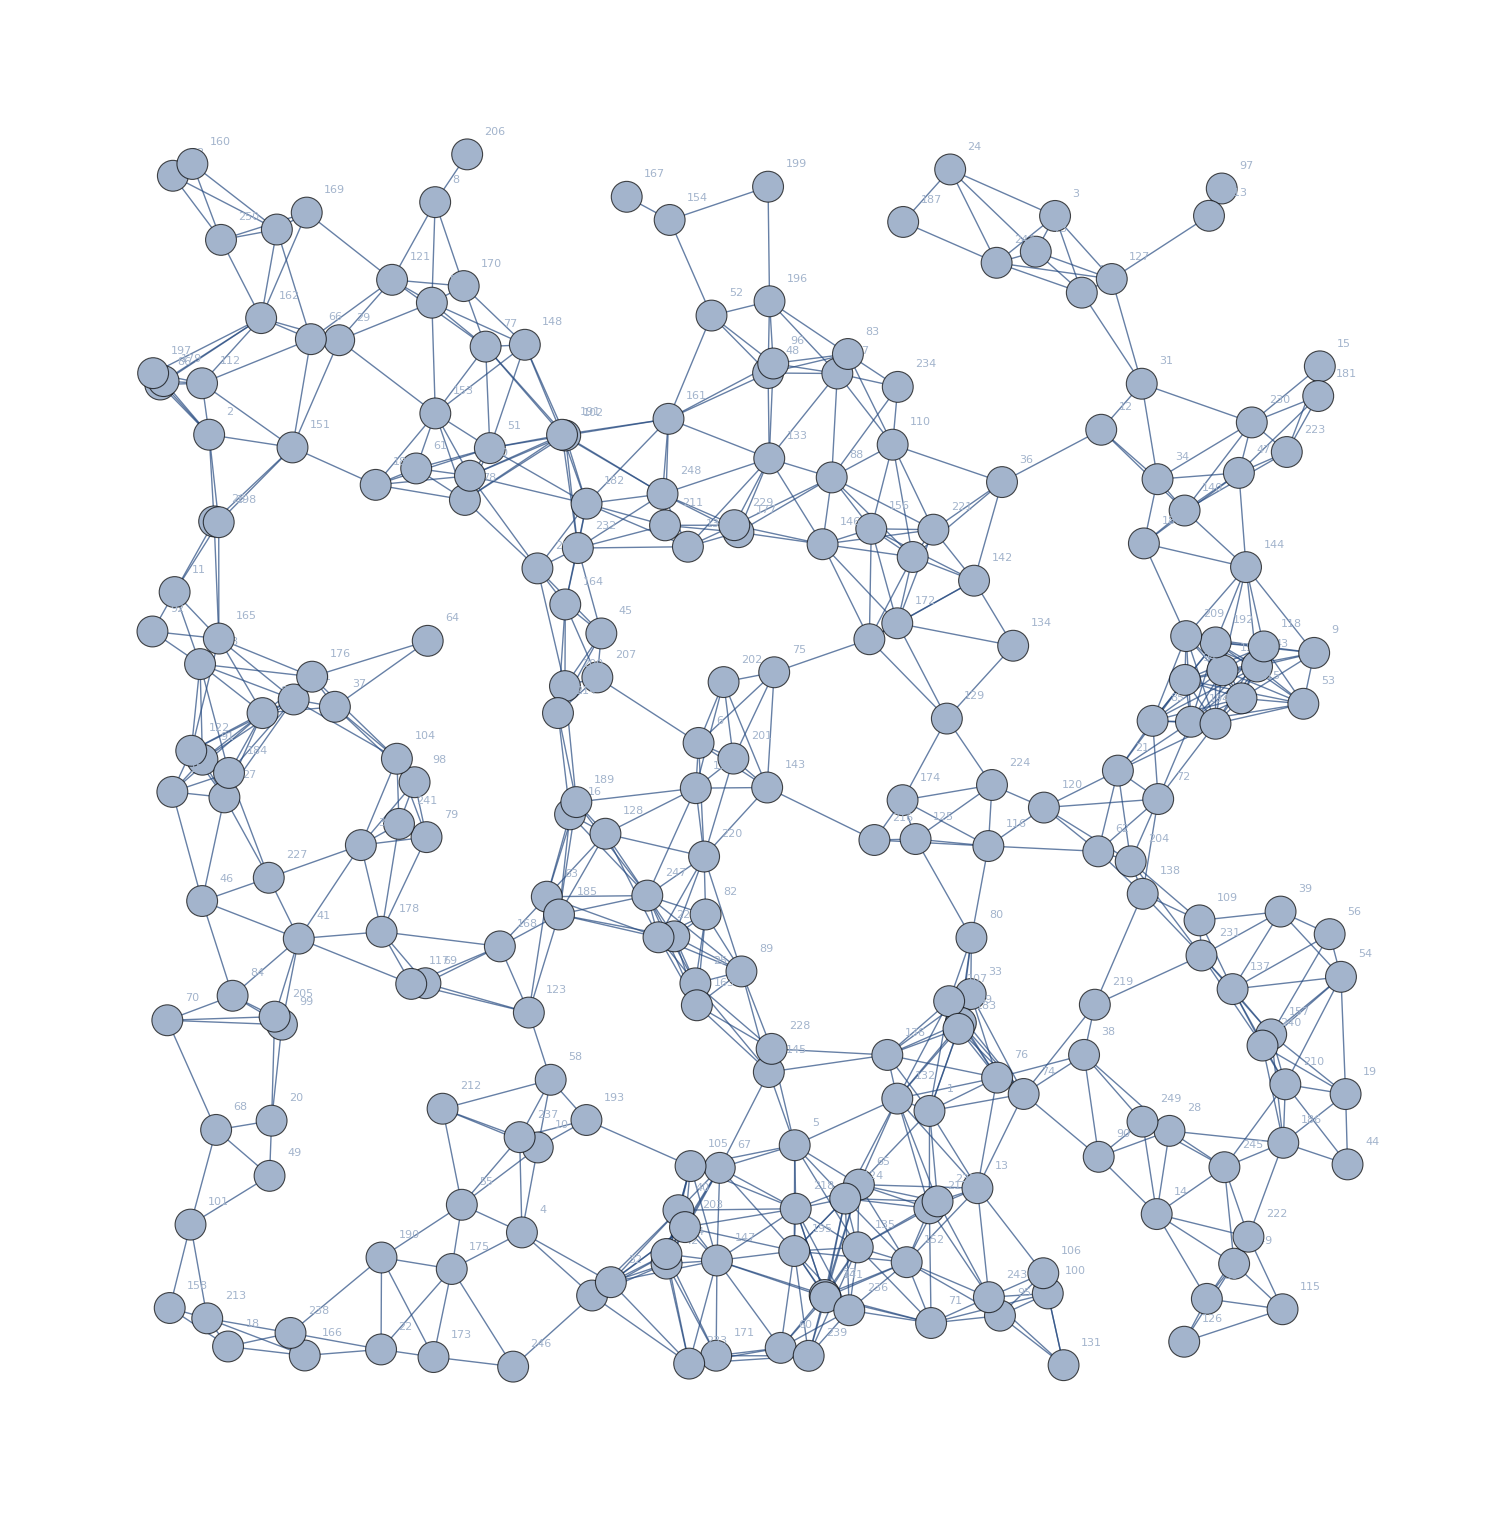

{{0.641666,0.211145},{0.0482287,0.768361},{0.745109,0.948617},{0.30591,0.111049},{0.530631,0.182912},{0.451447,0.51438},{0.363721,0.0590642},{0.234431,0.959997},{0.958561,0.588579},{0.318961,0.181078},{0.0198026,0.63871},{0.78314,0.772437},{0.681181,0.147512},{0.828848,0.126181},{0.963236,0.824694},{0.345555,0.455583},{0.627825,0.667611},{0.0638157,0.0170736},{0.984476,0.225059},{0.0996854,0.203121},{0.796887,0.491572},{0.189862,0.0146346},{0.555313,0.0595042},{0.658704,0.986935},{0.448798,0.316282},{0.0523471,0.696913},{0.060822,0.469531},{0.839412,0.194742},{0.15535,0.846231},{0.870176,0.0563052},{0.816535,0.810362},{0.379177,0.0700621},{0.67561,0.30747},{0.829537,0.731714},{0.17322,0.430199},{0.70141,0.729331},{0.15183,0.544162},{0.769003,0.257336},{0.930889,0.375416},{0.434838,0.12936},{0.122062,0.353133},{0.425072,0.085339},{0.91151,0.577385},{0.986068,0.167117},{0.371319,0.604607},{0.0424563,0.384126},{0.896558,0.736907},{0.50869,0.819215},{0.0980004,0.157668},{0.231725,0.877137},{0.279502,0.757307},{0.462082,0.866526},{0.94966,0.54664},{0.980656,0.321673},{0.256404,0.13384},{0.971346,0.356833},{0.565754,0.818783},{0.32961,0.236822},{0.66751,0.283754},{0.519092,0.0159289},{0.218794,0.74056},{0.780712,0.425072},{0.32641,0.387681},{0.228305,0.598516},{0.5835,0.150458},{0.132044,0.84709},{0.468899,0.164261},{0.0539758,0.195517},{0.226428,0.316392},{0.0137679,0.285868},{0.642984,0.0364073},{0.830062,0.468161},{0.729247,0.919171},{0.719259,0.225132},{0.513728,0.572622},{0.69736,0.238609},{0.275992,0.840958},{0.258934,0.714616},{0.227322,0.436783},{0.676222,0.353846},{0.431428,0.35502},{0.457237,0.373049},{0.574467,0.834869},{0.0675671,0.30605},{0.825468,0.532591},{0.00795783,0.80971},{0.0922183,0.538982},{0.561113,0.733163},{0.486743,0.326115},{0.781074,0.173354},{0.0427226,0.500574},{0.00152838,0.606224},{0.0183431,0.981718},{0.852072,0.566299},{0.699733,0.0424508},{0.512924,0.827029},{0.882439,0.97124},{0.217499,0.482027},{0.108198,0.282265},{0.739124,0.0607816},{0.0328869,0.117499},{0.341566,0.767715},{0.767153,0.885402},{0.202915,0.501356},{0.444819,0.165712},{0.735416,0.0774388},{0.657846,0.301598},{0.0407428,0.579354},{0.864127,0.368181},{0.611329,0.760129},{0.11787,0.550202},{0.0423812,0.810743},{0.871934,0.948735},{0.424948,0.0932676},{0.93254,0.0477568},{0.690168,0.429426},{0.214696,0.315826},{0.917092,0.59391},{0.592142,0.599834},{0.735922,0.461114},{0.19894,0.895982},{0.0334753,0.507922},{0.31161,0.292194},{0.572229,0.138956},{0.630205,0.435194},{0.851496,0.0209838},{0.79184,0.896655},{0.374709,0.439568},{0.655977,0.534444},{0.449136,0.477122},{0.752138,0.00167916},{0.615132,0.221303},{0.509657,0.748838},{0.710592,0.59447},{0.582567,0.0987406},{0.606929,0.257302},{0.89137,0.311555},{0.81732,0.390046},{0.442649,0.676061},{0.851837,0.70588},{0.555925,0.0576063},{0.678372,0.648065},{0.507935,0.477656},{0.90243,0.659259},{0.50931,0.243218},{0.553593,0.678113},{0.466567,0.087934},{0.308307,0.842459},{0.892628,0.0852614},{0.263103,0.734526},{0.116904,0.757875},{0.622896,0.0865496},{0.234556,0.785886},{0.427616,0.945307},{0.0179096,0.474059},{0.59369,0.690834},{0.923162,0.274256},{0.0157463,0.0487801},{0.883035,0.574183},{0.0344285,0.991455},{0.426664,0.781426},{0.0910682,0.864439},{0.450018,0.298222},{0.341602,0.628523},{0.0562255,0.600375},{0.127003,0.00965318},{0.392241,0.964392},{0.287739,0.346755},{0.128637,0.951375},{0.257955,0.890829},{0.465937,0.00946593},{0.615112,0.612977},{0.23306,0.00836839},{0.619498,0.467219},{0.248106,0.0809268},{0.13307,0.568967},{0.484256,0.688042},{0.190323,0.358785},{0.0106603,0.812551},{0.818305,0.678796},{0.961904,0.800227},{0.359152,0.711544},{0.665557,0.278819},{0.0646064,0.489661},{0.336465,0.373016},{0.933134,0.184899},{0.619975,0.943667},{0.185424,0.727035},{0.350724,0.465647},{0.190222,0.0903812},{0.338958,0.768309},{0.877399,0.597236},{0.359055,0.20368},{0.85708,0.53183},{0.530249,0.0957381},{0.50988,0.87831},{0.0020824,0.819091},{0.0561261,0.69629},{0.508681,0.97272},{0.341357,0.561209},{0.480116,0.501474},{0.472046,0.564531},{0.440239,0.115448},{0.807435,0.416817},{0.102179,0.288846},{0.260791,0.999355},{0.368046,0.568403},{0.318681,0.658222},{0.853107,0.602405},{0.934808,0.23312},{0.423805,0.693696},{0.240543,0.212979},{0.0466568,0.0402479},{0.335611,0.539015},{0.898673,0.551121},{0.596275,0.434401},{0.64157,0.130903},{0.531462,0.130572},{0.777887,0.298694},{0.455978,0.420782},{0.644892,0.690098},{0.904445,0.107533},{0.93603,0.754113},{0.693167,0.479734},{0.418424,0.354233},{0.877287,0.530188},{0.0973522,0.403274},{0.511614,0.262296},{0.480842,0.693816},{0.907189,0.778483},{0.865734,0.339206},{0.351972,0.674965},{0.443672,0.00296222},{0.61554,0.807765},{0.648336,0.136639},{0.575566,0.0469402},{0.304021,0.189567},{0.115269,0.0282215},{0.542141,0.0093787},{0.916014,0.265016},{0.204646,0.447685},{0.104026,0.937433},{0.69061,0.0576766},{0.696975,0.910013},{0.884636,0.1648},{0.298664,0.000472549},{0.409184,0.388599},{0.421764,0.719592},{0.817135,0.202338},{0.0580031,0.928896}}

Spatial.csv

SpatialCoords.csv

```mathematica
n=250;
randomGraph=RandomGraph[SpatialGraphDistribution[n,0.1],ImageSize->1500,VertexLabels->"Name"]

edgesList=GraphIntoEdgesList[randomGraph];
coords=GraphEmbedding[randomGraph]
Export["Spatial.csv",Cases[edgesList,{a_,b_,1.}->{a,b}]]
Export["SpatialCoords.csv",coords]
```

## Import Edges List

```mathematica
rawData=Import["edglst.txt","Table"];
edges=Flatten[{ToString[#[[1]]]->ToString[#[[2]]]}&/@Transpose[{rawData[[All,1]],rawData[[All,2]]}]];
weights=ConstantArray[1,edges//Length](*Chop/@rawData[[All,3]]*);
adjacencyMatrix=ConvertEdgesListToAdjacencyMatrix[edges,weights];
GraphTransitionsFrequencies[adjacencyMatrix];
```

exampleNetwork.png

```mathematica
rawData={#[[1]],#[[2]],1}&/@Import["Watts.csv"];
edges=Flatten[{ToString[#[[1]]]->ToString[#[[2]]]}&/@Transpose[{rawData[[All,1]],rawData[[All,2]]}]];
weights=Chop/@rawData[[All,3]];
adjacencyMatrix=ConvertEdgesListToAdjacencyMatrix[edges,weights];
edgeshape[e_,___]:={Arrowheads[{{.00,.5}}],Arrow[e]}
GraphTransitionsFrequenciesWithMax[{adjacencyMatrix[[1]]//UpperTriangularize,adjacencyMatrix[[2]]}, 10,VariableStyle->"LineColor",VertexLabelStyle->Opacity[0],LineThickness->.0025,EdgeShapeFunction->edgeshape,VertexSize->2,ImageSize->2000];
Rasterize[%,Background->None]//ColorNegate
Export["exampleNetwork.png",%]
```

-Graphics-

exampleNetwork.png

## Analysis

```mathematica
rawData=Import["edflst.txt","Table"];
imageSize=2000;
edges=Flatten[{ToString[#[[1]]]->ToString[#[[2]]]}&/@Transpose[{rawData[[All,1]],rawData[[All,2]]}]];
weights=ConstantArray[1,edges//Length](*Chop/@rawData[[All,3]]*);
adjacencyMatrix=ConvertEdgesListToAdjacencyMatrix[edges,weights];
GraphTransitionsFrequencies[adjacencyMatrix];
adjReady=Prepend[Transpose[Prepend[adjacencyMatrix[[1]],adjacencyMatrix[[2]]]],Flatten[{"X",adjacencyMatrix[[2]]}]]//Transpose;
Export["TwitterAdjacency.csv",adjacencyMatrix[[1]]]
```

TwitterAdjacency.csv

```mathematica
adjReady//Transpose//Length
```

916

OptionValue::nodef: Unknown option BaseStyle for GraphTransitionsFrequenciesWithMax.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

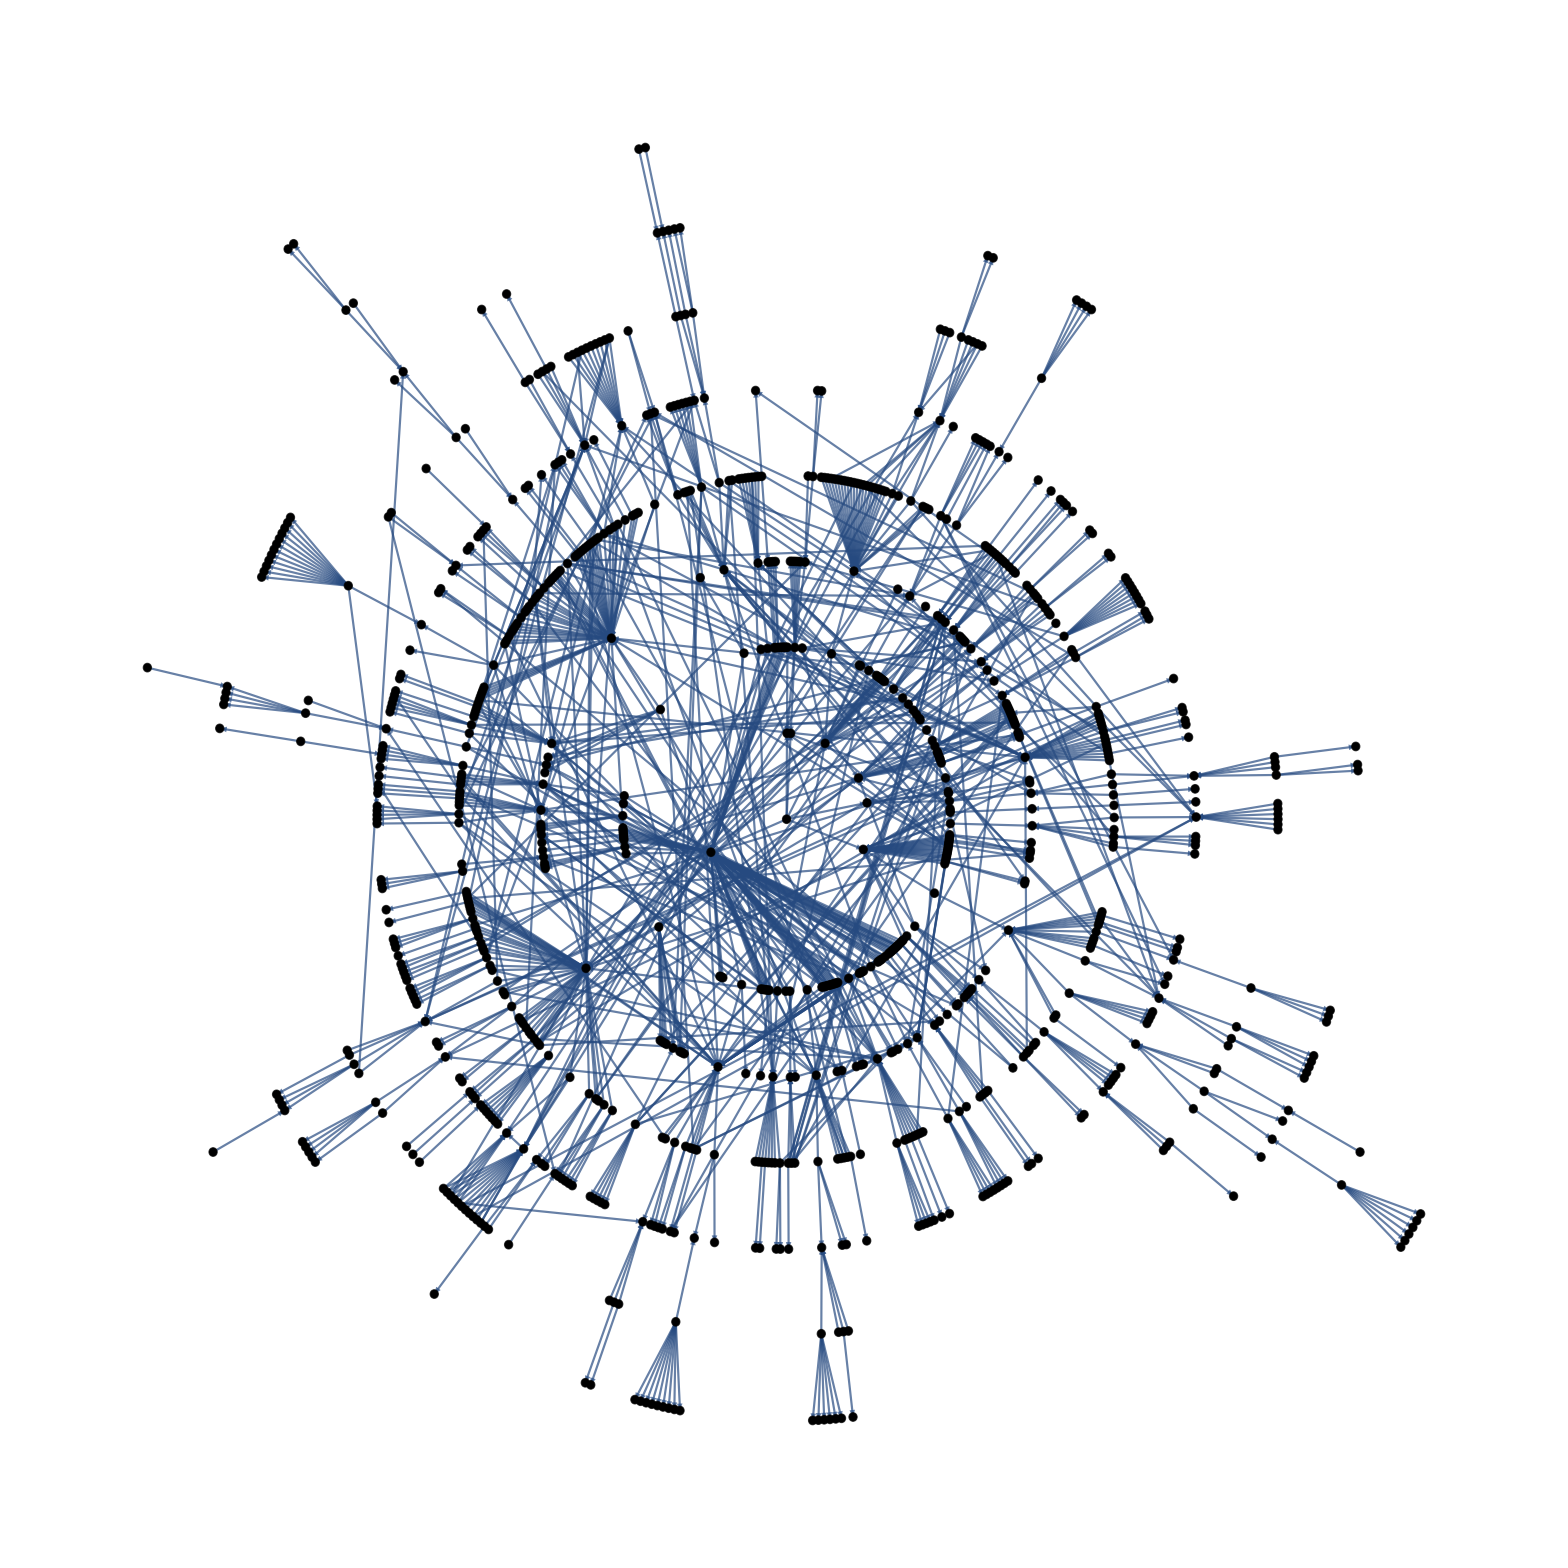

exampleNetwork.png

{{1,2,1.},{1,3,0.},{1,4,0.},{1,5,0.},{1,6,0.},{1,7,0.},{1,8,0.},{1,9,0.},{1,10,0.},{1,11,0.},{1,12,0.},{1,13,0.},{1,14,0.},{1,15,0.},{1,16,0.},{1,17,0.},{1,18,0.},{1,19,0.},{1,20,0.},{1,21,0.},{1,22,0.},{1,23,0.},{1,24,0.},{1,25,0.},{1,26,0.},{1,27,0.},{1,28,0.},{1,29,0.},{1,30,0.},{1,31,0.},{1,32,0.},{1,33,0.},{1,34,0.},{1,35,0.},836242,{915,881,0.},{915,882,0.},{915,883,0.},{915,884,0.},{915,885,0.},{915,886,0.},{915,887,0.},{915,888,0.},{915,889,0.},{915,890,0.},{915,891,0.},{915,892,0.},{915,893,0.},{915,894,0.},{915,895,0.},{915,896,0.},{915,897,0.},{915,898,0.},{915,899,0.},{915,900,0.},{915,901,0.},{915,902,0.},{915,903,0.},{915,904,0.},{915,905,0.},{915,906,0.},{915,907,0.},{915,908,0.},{915,909,0.},{915,910,0.},{915,911,0.},{915,912,0.},{915,913,0.},{915,914,0.}}
 |  |  |  |

twitter.csv

```mathematica
edgeshape[e_,___]:={Arrowheads[{{.00,.5}}],Arrow[e]}
graph=GraphTransitionsFrequenciesWithMax[
{adjacencyMatrix[[1]],adjacencyMatrix[[2]]}, 1,
VariableStyle->"None",
VertexLabelStyle->Opacity[0],
GraphLayout->"RadialEmbedding",
LineThickness->.001,
EdgeShapeFunction->edgeshape,
VertexSize->5,
VertexStyle->Lighter[Black,0],
ImageSize->{imageSize,imageSize},
BaseStyle->Directive[Lighter[Blue,.7],Thickness[.001],Opacity[.9],EdgeForm[Directive[White,Opacity[1],Thickness[.0025]]]]]
(*Rasterize[%,Background->None]//ColorNegate*)
Export["exampleNetwork.png",%]
edgesList=GraphIntoEdgesList[graph]
Export["twitter.csv",Cases[edgesList,{a_,b_,1.}->{a,b}]]
```

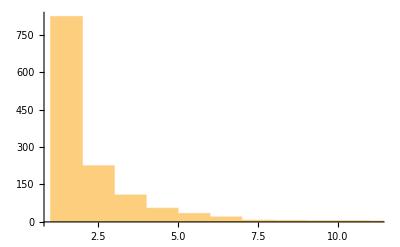

```mathematica
VertexDegree[graph]//Histogram
```

```mathematica
GraphPlot3D[adjacencyMatrix[[1]],ImageSize->2000,Method->Automatic]
```

-Graphics3D-

```mathematica
rawData=Import["edflst.txt","Table"];
edges=Flatten[{ToString[#[[1]]]->ToString[#[[2]]]}&/@Transpose[{rawData[[All,1]],rawData[[All,2]]}]];
weights=ConstantArray[1,edges//Length](*Chop/@rawData[[All,3]]*);
adjacencyMatrix=ConvertEdgesListToAdjacencyMatrix[edges,weights];
GraphTransitionsFrequencies[adjacencyMatrix];
```

```mathematica
flatEdges={ToString[#[[1]]],ToString[#[[2]]]}&/@Transpose[{rawData[[All,1]],rawData[[All,2]]}]
minValue=Min[Flatten[{flatEdges}]//ToExpression]
zeroed={
ToExpression[flatEdges[[All,1]]]-minValue,
ToExpression[flatEdges[[All,2]]]-minValue
}//Transpose;
flatEdges={ToString[#[[1]]],ToString[#[[2]]]}&/@zeroed;
Export["flat2.csv",flatEdges];
```

122254.

```mathematica
graph=adjacencyMatrix[[1]]//AdjacencyGraph//UndirectedGraph;
centrality=BetweennessCentrality[graph];
HighlightGraph[graph,
VertexList[graph],
VertexSize-> Thread[VertexList[graph]-> Rescale[%,{0,centrality//Max},{0,50}]],
GraphLayout->"RadialEmbedding",
VertexStyle->Black,
GraphHighlightStyle->Thick,
ImageSize->imageSize
]
Export["exampleNetwork2.png",%]
```

-Graphics-

exampleNetwork2.png

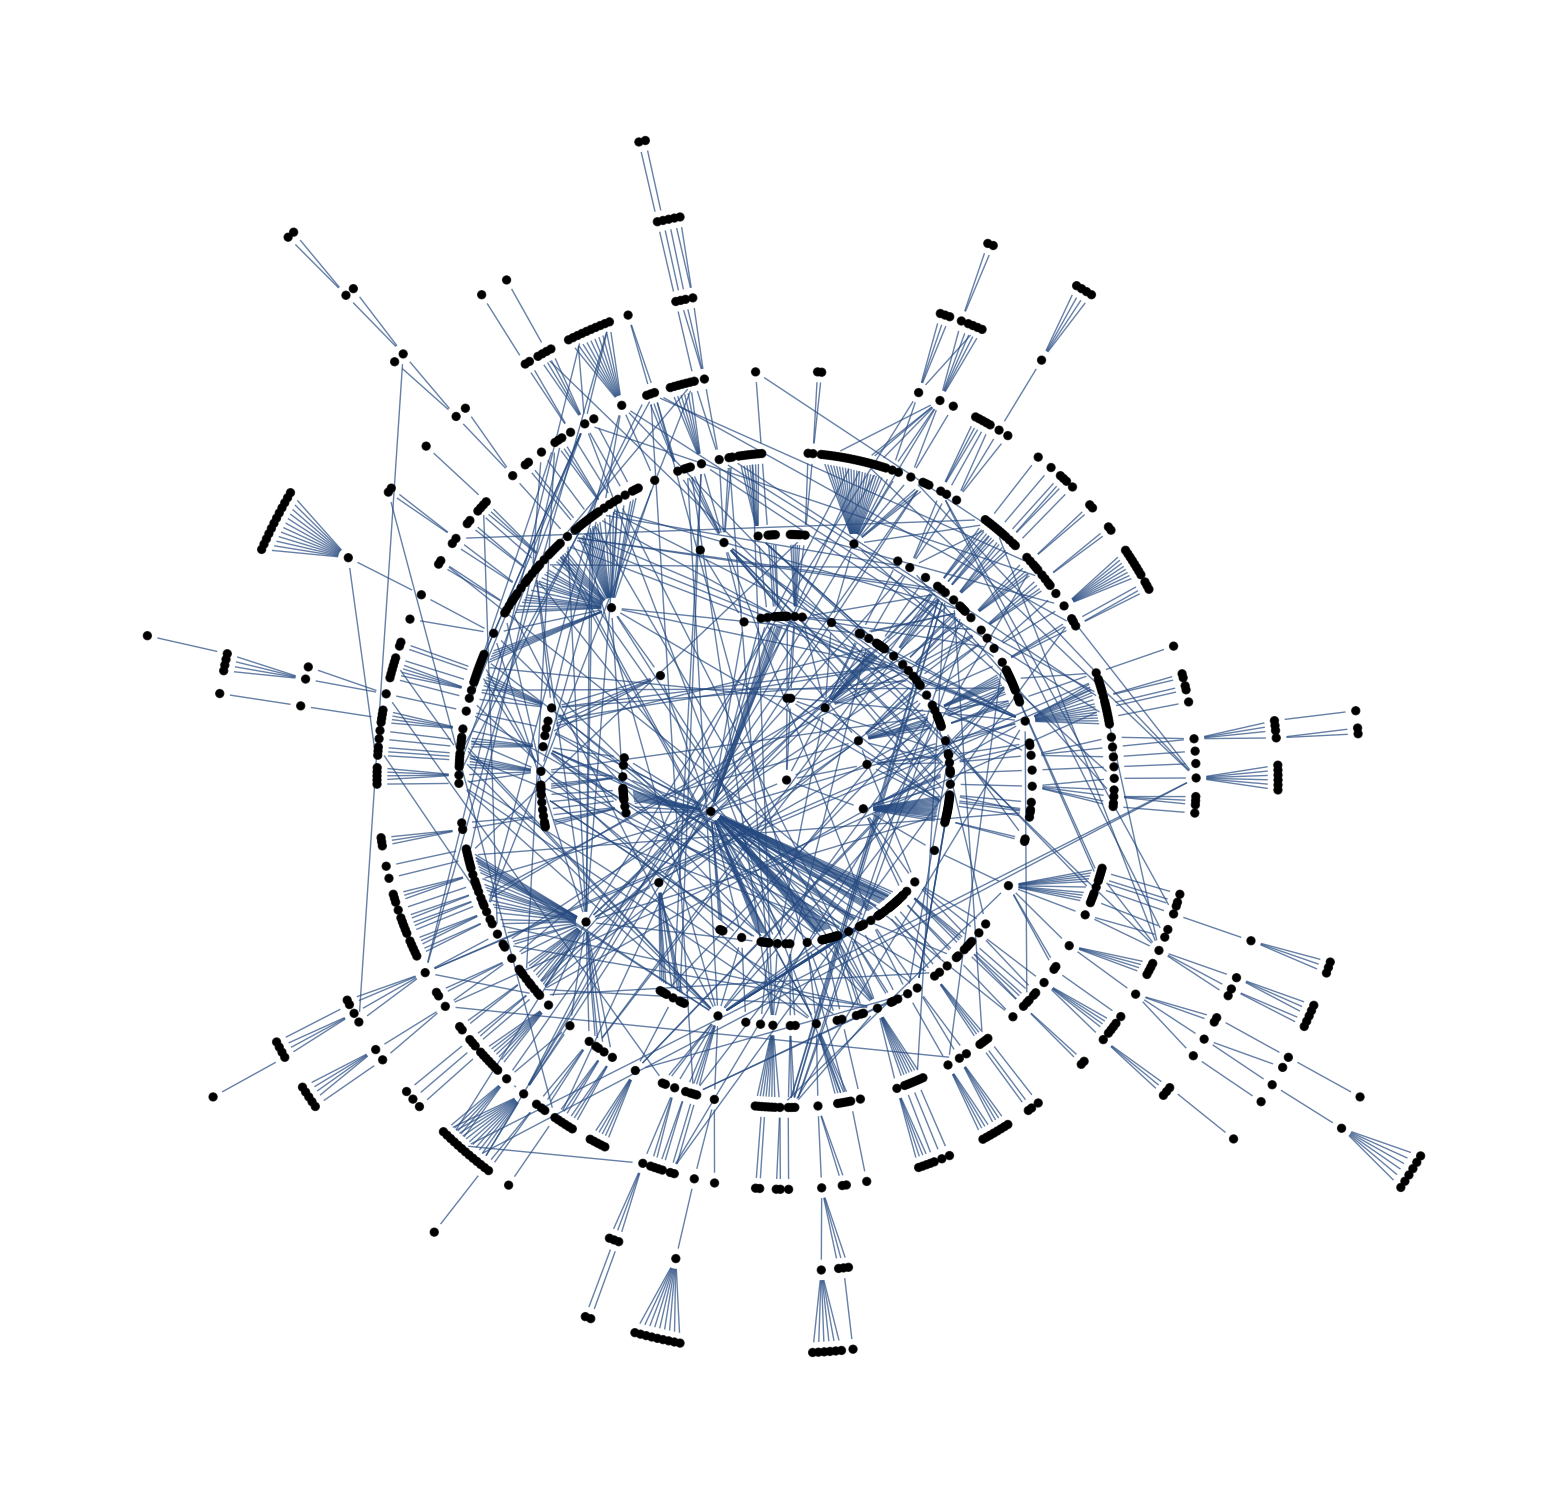

exampleNetwork.png

```mathematica
graph=adjacencyMatrix[[1]]//AdjacencyGraph//UndirectedGraph;
centrality=BetweennessCentrality[graph];
HighlightGraph[graph,
VertexList[graph],
VertexSize-> Thread[VertexList[graph]-> Rescale[%,{0,100000},{5,5}]],
GraphLayout->"RadialEmbedding",
VertexStyle->Black,
GraphHighlightStyle->Thick,
ImageSize->imageSize
]
Export["exampleNetwork.png",%]
```